```mathematica
Clear[i1,i2]
```

```mathematica
M = 25;
Ml = 10;
L = 0.8;
b1 = 5;
b2 = 5;
Ka = 52.52;
kt1 = 61;
kt2 = 61;
ke1 = 49.6;
ke2 = 49.6;
La1 = 5.07 * 10^-3;
La2 = 5.07* 10^-3;
Ra1 = 8.4;
Ra2 = 8.4;
```

```mathematica
J[l1_, l2_]:= M/3(l1^2-l1 l2 + l2^2)
a31[l1_, l2_]:= (-Ka l1)/(J[l1,l2]l1 + J[l1,l2]l2)
a32[l1_,l2_]:= (Ka l1)/(J[l1,l2]l1 + J[l1,l2]l2)
a33[l1_,l2_]:= (-b1 L)/(M l1 + M l2)- (b1 L l1^2)/(J[l1,l2]l1 + J[l1,l2]l2)
a34[l1_,l2_]:=(-b2 L)/(M l1 + M l2)- (b2 L l1 l2)/(J[l1,l2]l1 + J[l1,l2]l2)
a35[l1_,l2_]:=(kt1 L)/(M l1 + M l2)- (kt1 L l1 l2)/(J[l1,l2]l1 + J[l1,l2]l2)
a36[l1_,l2_]:=(kt2 L)/(M l1 + M l2)- (kt2 L l1 l2)/(J[l1,l2]l1 + J[l1,l2]l2)
a41 [l1_,l2_]:=(Ka l2)/(J[l1,l2]l1 + J[l1,l2]l2)
a42[l1_,l2_]:=(-Ka l2)/(J[l1,l2]l1 + J[l1,l2]l2)
a43[l1_,l2_]:=(-b1 L)/(M l1 + M l2)- (b1 L l1 l2)/(J[l1,l2]l1 + J[l1,l2]l2)
a44[l1_,l2_]:=(-b2 L)/(M l1 + M l2)- (b2 L l2^2)/(J[l1,l2]l1 + J[l1,l2]l2)
a45[l1_,l2_]:=(kt1 L)/(M l1 + M l2)- (kt1 L l1 l2)/(J[l1,l2]l1 + J[l1,l2]l2)
a46[l1_,l2_]:=(kt2 L)/(M l1 + M l2)- (kt2 L l2^2)/(J[l1,l2]l1 + J[l1,l2]l2)
```

```mathematica
A[l1_,l2_] := {{0,0,1,0,0, 0},{0,0,0,1,0,0},{a31[l1,l2],a32[l1,l2],a33[l1,l2],a34[l1,l2],a35[l1,l2],a36[l1,l2]},{a41[l1,l2],a42[l1,l2],a43[l1,l2],a44[l1,l2],a45[l1,l2],a46[l1,l2]},{0,0,-ke1/La1,0,-Ra1/La1,0},{0,0,0,-ke2/La2,0,-Ra2/La2}};
```

```mathematica
B = {{0,0},{0,0},{0,0},{0,0},{1/La1,0},{0,1/La2}};
```

```mathematica
CC = {{1,0,0,0,0,0},{0,1,0,0,0,0}};
```

```mathematica
u = {{u1},{u2}};
u1 = 1;
u2 = 1;
i1[t_] := 10Sin[50t];
i2 [t_]:= 10Sin[50t];
```

```mathematica
x = {{y1[t]},{y2[t]},{y1'[t]},{y2'[t]},{i1[t]},{i2[t]}};
derX = {{y1'[t]},{y2'[t]},{y1''[t]},{y2''[t]},{i1'[t]},{i2'[t]}};
```

```mathematica
l1 =0.2;
l2 = L - l1;
rightPart = A[l1,l2].x+  B . u;
```

```mathematica
sol1 = NDSolve[{derX[[3,1]]==rightPart[[3,1]], derX[[4,1]]==rightPart[[4,1]],y1[0]==0, y2[0]==0, y1'[0]==0,y2'[0]==0},{y1,y2},{t,0,10}]
```

{{y1→InterpolatingFunction[…],y2→InterpolatingFunction[…]}}

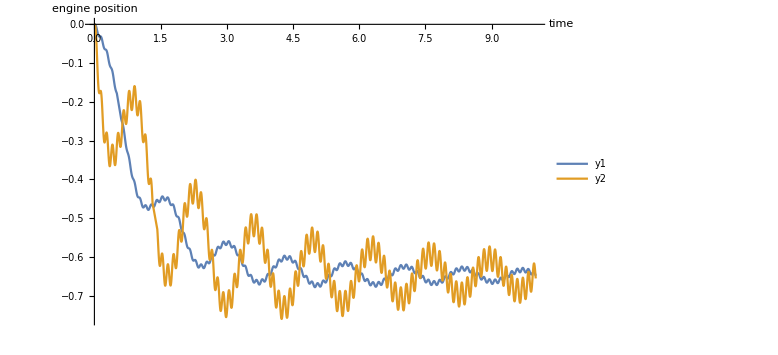

```mathematica
Plot[{y1[t]//.sol1,y2[t]/.sol1},{t,0,10},AxesLabel->{"time", "engine position"},PlotLegends->{"y1","y2"},ImageSize->Large]
```